```mathematica
a0={"u1","u2","u3","u4",1," "}
a1={-3,3,2,-2,12,"s1"}
a2={2,-2,5,-5,20,"s2"}
a3={-1,1,-6,6,-3,"s3"}
a4={1,-1,-2,2,4,"s4"}
a5={12,-12,2,-2,60,"s5"}
z={6,-6,1,-1,-2,"z"}
a = {a0,a1,a2,a3,a4,a5,z}
Print[MatrixForm[a]]
```

{u1,u2,u3,u4,1, }

{-3,3,2,-2,12,s1}

{2,-2,5,-5,20,s2}

{-1,1,-6,6,-3,s3}

{1,-1,-2,2,4,s4}

{12,-12,2,-2,60,s5}

{6,-6,1,-1,-2,z}

{{u1,u2,u3,u4,1, },{-3,3,2,-2,12,s1},{2,-2,5,-5,20,s2},{-1,1,-6,6,-3,s3},{1,-1,-2,2,4,s4},{12,-12,2,-2,60,s5},{6,-6,1,-1,-2,z}}

(u1 | u2 | u3 | u4 | 1 |  
-3 | 3 | 2 | -2 | 12 | s1
2 | -2 | 5 | -5 | 20 | s2
-1 | 1 | -6 | 6 | -3 | s3
1 | -1 | -2 | 2 | 4 | s4
12 | -12 | 2 | -2 | 60 | s5
6 | -6 | 1 | -1 | -2 | z)

```mathematica
g1[x1_, x2_] := -3x1+2x2; b1 = -12; 
g2[x1_, x2_] := 2x1+5x2; b2 = -20; 
g3[x1_, x2_] := -x1-6x2; b3 = 3; 
g4[x1_, x2_] := 1x1-2x2; b4= -4; 
g5[x1_, x2_] := 12x1+2x2;b5 = -60;
```

```mathematica
g1[x1_]=x2/.Solve[g1[x1,x2] == b1] [[1,1]] 
g2[x1_]=x2/.Solve[g2[x1,x2] == b2] [[1,1]] 
g3[x1_]=x2/.Solve[g3[x1,x2] == b3] [[1,1]] 
g4[x1_]=x2/.Solve[g4[x1,x2] == b4] [[1,1]] 
g5[x1_]=x2/.Solve[g5[x1,x2] == b5] [[1,1]] 

Plot[{g1[x],g2[x],g3[x],g4[x],g5[x]}, {x,-12,12}, PlotHighlighting->None, AspectRatio->Automatic, PlotRange-> {-15,15}, PlotLegends -> Automatic]
```

-6+(3 x1)/2

-4-(2 x1)/5

-1/2-x1/6

2+x1/2

-30-6 x1

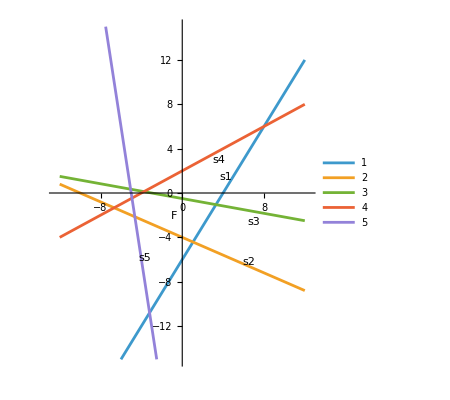

```mathematica
pivot[iStar_, jStar_, tab_]:=(
newTab =tab; 
tableauDimensions = Dimensions[tab];
rows =tableauDimensions[[1]]; 
cols = tableauDimensions[[2]];
newTab[[1,jStar]]= tab[[iStar, cols]]; 
newTab[[iStar,cols]] = tab[[1, jStar]]; 
For[i=2; i< rows, i++, 
For[j=1, j<cols, j++, 
{
If[i == iStar && j == jStar, newTab[[i,j]] = 1/tab[[iStar,jStar]]];
If[i == iStar && j!= jStar, newTab[[i,j]] = -tab[[i,j]]/tab[[iStar,jStar]]];
If[i != iStar && j== jStar, newTab[[i,j]] = tab[[i,j]]/tab[[iStar,jStar]]];
If[i != iStar && j!= jStar, newTab[[i,j]] = tab[[i,j]]-((tab[[i,jStar]]tab[[iStar,j]])/tab[[iStar,jStar]])];
}
]
]

Return[newTab]
)

b = pivot[3,2,a];
Print[MatrixForm[b]];
```

Null Return[{{u1,s2,u3,u4,1, },{-3,3,2,-2,12,s1},{2,-2,5,-5,20,u2},{-1,1,-6,6,-3,s3},{1,-1,-2,2,4,s4},{12,-12,2,-2,60,s5},{6,-6,1,-1,-2,z}}]